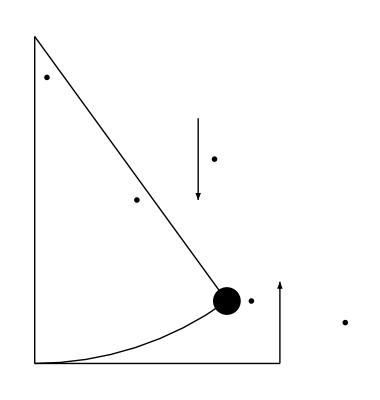

```mathematica
ClearAll[pendulumPhaseSpaceFig1, mp, o]

r = 4;
o = {0,r};
zmp = -I r Exp[I 0.4 Pi/2];
mp = o + {zmp // Re, zmp // Im };
pendulumPhaseSpaceFig1 = Graphics[{
Thick,
Arrowheads -> Medium,
Line[{{0,0}, {0, 4}}],
Line[{{0,0}, {3, 0}}],
Arrow[ {{2, 3}, {2, 2}}],
Arrow[ {{3, 0}, {3, 1}}],
Line[{{0, 4}, mp}],
PointSize -> 0.05,
Point[mp],
Text[MaTeX["\\theta"], {0.15, 3.5}],
Text[MaTeX["m"], mp + {0.3, 0}],
Text[MaTeX["l"], {2.5/2, 2}],
Text[MaTeX["z = l (1 - \\cos\\theta)"], {3.8, 0.5}],
Text[MaTeX["g"], {2.2, 2.5}],
Circle[o, r, {-Pi/2, -Pi/2 + 0.4 Pi/2}]
}]
```

```mathematica
peeters`exportForLatex["pendulumPhaseSpaceFig1",pendulumPhaseSpaceFig1]
```

{pendulumPhaseSpaceFig1.eps,pendulumPhaseSpaceFig1pn.png}